# Interference of Sound Waves

## Lab Report

Names: Aryan Malhotra and Andrew Bassett
Section: H5
Date: 1/31/2025

## Purpose

To measure the wavelength, frequency, and propagation speed of ultrasonic sound waves and to observe interference phenomena with ultrasonic sound waves.

## Apparatus

Oscilloscope, function generator, transducers, meter stick, angle board.

## Readings

### Sound Waves

In this experiment we deal with sound waves, produced by and detected with ultrasonic transducers. Sinusoidal waves can be characterized by the following parameters:
- Wavelength: λ,
- Frequency: f,
- Period: T=1/f,
- Wave propagation speed: c=f λ=λ/T,
- The speed of sound through air at 20 °C = 344  m/s.

### Ultrasonic Transducers

A transducer is a device that transforms one form of energy into another, for example, a microphone (sound to electric) or loudspeaker (electric to sound). In this experiment the transducer is a “piezoelectric” crystal which converts electrical oscillations into mechanical vibrations that make sound. The piezoelectric material contracts (or expands) a small amount when a voltage is applied across the crystal. Conversely, if its dimension is changed, it produces voltage. The crystal has a natural resonance frequency, like a bell, at which it will vibrate when struck. If the frequency of the voltage applied to the piezoelectric crystal is the same as its natural frequency, the crystal will settle into steady large amplitude oscillations that produce high intensity sound waves. The oscillating frequency of the transducers you will use is near 40 kHz which is beyond what can be heard by the human ear (about 20 kHz).

### Oscilloscope

The oscilloscope is an electronic device that acts as a voltmeter that can respond very rapidly to changes in the applied voltage.  It is used here to display a graph of the instantaneous voltage applied to the crystal as a function of time.

### Interference of Waves

Figure 1, on the next page, is a drawing of the basic concept of interference of coherent waves from two point sources. S1 and S2 are wave sources oscillating in phase (because the two transducers are driven by the same voltage signal generator) and separated by distance d.  P is the place where we place a detector.  At point P the path difference to S_1 and to S_2, is the distance S_2P - S_1P. When this path difference is an integral multiple of the wavelength λ, waves arriving at P from S_1 and S_2 will be in phase and will interfere constructively,
(1)	S_1 P -S_2 P=n λ,
where n = 0, 1, 2, ...  is referred to as the order of the particular maximum. Note that constructive interference gives maximum intensity.
If we can assume that S_1P and S_2P >> d and λ in equation (1), then we see from fig. 1 that one can write,
(2)	d sin θ_max=n λ.

Figure 1. Two sources S_1 and S_1 create an interference at point P.


-Graphics-

## Procedure

The setup will be more or less like the one shown in fig. 2. A variable frequency signal generator drives one ultrasonic transducer; its output is also applied to channel B of the oscilloscope. (Later in the experiment two transmitting transducers will be connected to channel B.) The output of a second receiving ultrasonic generator is applied to channel A of the scope.  Channel B’s trace (pattern of the oscilloscope) shows the sinusoidal voltage applied to the transmitting generator; channel A’s trace shows the sinusoidal voltage produced by the receiving ultrasonic crystal.

Figure 2. The setup of the experiment with one transmitter.

-Graphics-

Warning:
Do not exchange your transducers with those from other tables; your three transducers are a matched set.

## Dialog:

## Part I. Measuring Frequency & Wavelength

### Step 1. Tuning Piezoelectric Crystal & Measuring Frequency

- Set the signal generator to a frequency of 40 kHz. Adjust the scope controls (trigger, beam intensity, vertical amplification, and horizontal sweep rate) so that trace A shows several, steady cycles of the sine waves. Place the transmitting transducer facing the receiver at a distance of a few centimeters. If you think the transducers are not functioning (nothing on trace A), it is most likely that the function generator is not set at the exact resonance frequency. Vary the frequency around 38 to 42 kHz. You should tune to resonance when the signal getting through to the receiving transducer (trace A) reaches a maximum.
- Measure the period of oscillation directly from the oscilloscope’s screen. To make the period measurement as accurate as possible, measure the time interval corresponding to several complete oscillations and try to use the most available area on the oscilloscope screen.

Hints:
> The error of the “total time interval” is the resolution of your oscilloscope screen. You can use half the size of the smallest divisions. The y-axis on the oscilloscope will be the voltage and x-axis will be the time. The units are written on the 	bottom of the screen. These units show the scale for each square on the screen.
> When you divide to the number of counts, you need to divide both the number and its error to get T_o±Δ T_o.
> To find the error in f_o you need to use the propagation of error.

Suggestions:
+ Always keep your measurements or calculation results using properly named variables. For example, fo variable name for f_o in kHz and dfo variable name for Δ f_o in kHz. When filling the table to report f_o, use
PlusMinus[NumberForm[fo,?], NumberForm[dfo,1]],
replacing ? with number of significant figures you want to use. Usually we use one sig. fig. for the error. We always must match the least significant figures between the error and the number (last digit on the right) and this is how you decide on number of significant figures.
+ Try to keep your report notebook tidy and avoid copying or retyping numbers. Use semicolon ; at the end of calculations as much as possible. The final results will be saved in variables and will be shown on the table. So avoid having Output cells for numerical calculations, as much as you can.
+ If a formula is simple and you won’t need the variable later, you can even do the calculation inside the PlusMinus command when writing the table.
For example, PlusMinus[NumberForm[(x-y)/n, 3], NumberForm[dx/n, 1]].

Answer:
On the oscilloscope, we could see exactly 10 major divisions corresponding to 4 periods of the wave. The wavelength, therefore, was 25 divisions long.
Each division was 10 μs wide hence wave had the time period of roughly 10*10/4 = 25 μs.

Since frequency = 1/ time period, that means the frequency was 40 kHz

By considering the speed of light to be 343, we can use v = wavelength * frequency to calculate the wavelength.


"Quantity" | "Value ± Error"
"Period (To, μs)" | "25."±"0.25"
"Frequency (fo, kHz)" | "40."±"0.0004"
"Wavelength (λo, mm)" | "8.575"±"0.00009"

```mathematica
(*Given Data*)
totalTime=100*10^-6; (*s*)
resolution=totalTime/50/2; (*Error in total time interval - there were 50 total divisions and the hint asks us to take half the size of the smallest division to be the error*)
n=4; (*Number of periods counted*)
v=343.0; (*Speed of sound in m/s*)

(*Total Period and Time period error Error*)
to=totalTime/n; (*Total period of the wave in seconds*)
deltaTo=resolution/n; (*Error in single period*)

(*Frequency and Error*)
fo = 1/to;
deltaFo=fo*(deltaTo/to); (*Propagation of error for frequency*)

(*Wavelength and Error*)
wavelengtho=v/fo; (*Wavelength in meters*)
deltaWavelengtho=wavelengtho*(deltaFo/fo); (*Error in wavelength*)

(*Display Results in Table Format*)
Grid[{{"Quantity","Value ± Error"},{"Period (To, μs)",PlusMinus[NumberForm[N[to * 10^(6)],4],NumberForm[N[deltaTo*10^6],2]]},{"Frequency (fo, kHz)",PlusMinus[NumberForm[N[fo/1000],5],NumberForm[N[deltaFo/1000],1]]},{"Wavelength (λo, mm)",PlusMinus[NumberForm[N[wavelengtho*1000],4],NumberForm[N[deltaWavelengtho*1000],1]]}}]
```

Quantity | Value ± Error
Period (To, μs) | 25.±0.25
Frequency (fo, kHz) | 40.±0.4
Wavelength (λo, mm) | 8.575±0.09

```mathematica
Grid[{{Text["Table 1. Measuring Frenquency Using Oscilloscope"],SpanFromLeft},
{"# of periods counted","total time interval (μs)","T_o±ΔT_o (μs)","f_o±Δf_o (kHz)"},
{n,PlusMinus[NumberForm[N[totalTime*10^6],5],NumberForm[N[resolution*10^6],1]],PlusMinus[NumberForm[N[to*10^6],4],NumberForm[N[deltaTo*10^6],2]],PlusMinus[NumberForm[N[fo/1000.0],5],NumberForm[N[deltaFo/1000.0],1]]}},Frame->All]
```

Table 1. Measuring Frenquency Using Oscilloscope |  |  | 
# of periods counted | total time interval (μs) | T_o±ΔT_o (μs) | f_o±Δf_o (kHz)
4 | 100.±1. | 25.±0.25 | 40.±0.4

- Compare the frequency f_o determined with the oscilloscope with the frequency f_sg of the signal generator.
- Also the oscilloscope writes the frequency on the bottom right corner, which we will call f_o^auto. Record your result on the table below.

Hints:
> The Δ f_sg is given by the precision of the signal generator. In other words, ±1 times the value of the least significant digit placeholder. Similarly for Δ f_o^auto. If they are not steady and the number on screen changes, using how much they change you can estimate their errors.
> To find Δ(f_o/f_sg) you need to use propagation of errors.

Answer:
The signal generator showed 40.00 kHz Hence, the least count/precision is 0.01 kHz for fsg
The receiver read 39.9969 kHz, Hence the least count/precision is 0.0001 kHz for f0

```mathematica
(* This is an Input cell in case you need *)
(*Given Data*)
fsg=40000; (*Signal generator frequency (Hz)*)
deltaFsg=10; (*Precision of the signal generator (Hz)*)

fauto=39997; (*Auto frequency from oscilloscope display (Hz)*)
deltaFauto=1; (*Precision of auto frequency (Hz)*)

(*Calculate Ratio and Propagation of Error*)
ratio=fo/fsg; (*Ratio of measured to generated frequency*)
deltaRatio=ratio*Sqrt[(deltaFo/fo)^2+(deltaFsg/fsg)^2]; (*Error in ratio*)
```

```mathematica
Grid[{{Text["Table 2. Measured Frenquencies"],SpanFromLeft},
{"f_o±Δf_o (kHz)","f_sg±Δf_sg (kHz)","f_o/f_sg±Δ(f_o/f_sg)","f_o^auto±Δf_o^auto (kHz)"},
{PlusMinus[NumberForm[N[fo/1000],6],NumberForm[N[deltaFo/1000],1]],PlusMinus[NumberForm[N[fsg/1000],4],NumberForm[N[deltaFsg/1000],2]],PlusMinus[NumberForm[ratio,5],NumberForm[N[deltaRatio],3]],PlusMinus[NumberForm[N[fauto/1000],5],NumberForm[N[deltaFauto/1000],1]]}
},Frame->All]
```

Table 2. Measured Frenquencies |  |  | 
f_o±Δf_o (kHz) | f_sg±Δf_sg (kHz) | f_o/f_sg±Δ(f_o/f_sg) | f_o^auto±Δf_o^auto (kHz)
40.±0.4 | 40.±0.01 | 1±0.01 | 39.997±0.001

### Step 2. Measuring Wavelength & Calculating Sound Speed

The transmitting and receiving transducer stands fit over, and can slide along, a meter stick. With both transducers fixed in position, the two sinusoidal traces on the scope are steady.

#### Question 1. - Explain what happens to the scope trace from the receiving transducer when you move the receiving transducer away from the transmitting transducer.

#### Answer 1. - The values in the scope trace oscillate periodically, i.e. as we move the receiving transducer, it reads increasing and decreasing magnitudes of signals due to the waves interfering constructively in some regions and destructively in others in an alternative fashion.

- Measure the wavelength by slowly shifting the receiving transducer a known distance away from the transmitter while noting on the oscilloscope screen by how many complete cycles of relative phase the wave pattern shifts. Do not choose just one cycle, but as many cycles as can conveniently be measured along the meter stick.
x_i is the initial position of the movable sensor and x_f is the final position, and D=x_f-x_i.

Hints:
> The error Δ D can be calculated by propagation of errors, Δ D=√((Δ x_i)^2+(Δ x_f)^2).
> Again, take the count error to be zero. So when you have a formula like x=X/n where n is a count number, then Δ x=Δ X/n.

Answer:
x_i = 40 mm ± 1mm
x_f = 125 mm ± 1mm
# of periods = 10

```mathematica
(* This is an Input cell in case you need *)
(*Given Data*)
xi=40; (*Initial position (mm)*)
deltaXi=1; (*Error in initial position (mm)*)

xf=125; (*Final position (mm)*)
deltaXf=1; (*Error in final position (mm)*)

nPeriods=10; (*Number of periods measured*)

(*Calculate D and its error*)
d=xf-xi; (*Displacement (mm)*)
deltaD=Sqrt[deltaXi^2+deltaXf^2]; (*Error in displacement (mm)*)

(*Calculate wavelength and its error*)
lambdaO=d/nPeriods; (*Wavelength (mm)*)
deltaLambdaO=deltaD/nPeriods; (*Error in wavelength (mm)*)
```

```mathematica
Grid[{{Text["Table 3. Measuring Wavelength Using Oscilloscope"],SpanFromLeft},
{"# of wavelength moved on OSC","x_i (mm)","x_f (mm)", "D±ΔD (mm)", "λ_o±Δλ_o (mm)"},
{nPeriods,PlusMinus[NumberForm[xi,2],NumberForm[deltaXi,1]],PlusMinus[NumberForm[xf,3],NumberForm[deltaXf,1]],PlusMinus[NumberForm[d,4],NumberForm[N[deltaD],1]],PlusMinus[NumberForm[N[lambdaO],4],NumberForm[N[deltaLambdaO],2]]}
},Frame->All]
```

Table 3. Measuring Wavelength Using Oscilloscope |  |  |  | 
# of wavelength moved on OSC | x_i (mm) | x_f (mm) | D±ΔD (mm) | λ_o±Δλ_o (mm)
10 | 40±1 | 125±1 | 85±1. | 8.5±0.14

- Use the measured frequency of ultrasonic oscillations from step 1 and the wavelength from this step to compute the speed of sound through air.
The frequency f_o measured with the scope is more accurate than the frequency readings on the signal generator.
- Record your results on the table below.
- Compare your computed value with the standard value of c = 344 m/s for dry air at 20°C. When an error is not given take ±1 times least significant digit to be the error. So in fact, c = 344 ± 1 m/s for dry air at 20°C.

Answer:
"Frequency (fo, Hz)" | =  "40."±"0.0004"
"Wavelength (λo, mm)" | = 8.5 ± 0.14
v = λ ν

```mathematica
(* This is an Input cell in case you need *)
(*STEP 1:Given Data*)

fo;
deltaFo;


(*Wavelength and Error from STEP 2*)
lambdao = N[lambdaO];
deltalambdao = N[deltaLambdaO];

(*Compute Speed of Sound*)
cExp=fo*lambdao/1000; (*Experimental speed of sound (m/s)*)
deltaCExp=cExp*Sqrt[(deltaFo/fo)^2+(deltaLambdaO/lambdao)^2]; (*Error in speed*)

(*Standard Speed of Sound*)
cStd=344; (*Standard value of c (m/s)*)
deltaCStd=1; (*Error in standard speed (m/s)*)

(*Ratio of Experimental to Standard Speed*)
ratioC=cExp/cStd; (*Ratio of experimental to standard speed*)
deltaRatioC=ratioC*Sqrt[(deltaCExp/cExp)^2+(deltaCStd/cStd)^2]; (*Error in ratio*)
```

```mathematica
Grid[{{Text["Table 4. Measured Wavelength & Sound Speed"],SpanFromLeft},
{"f_o±Δf_o (kHz)","λ_o±Δλ_o (mm)","c_exp±Δc_exp (m/s)","c_exp/c±Δ(c_exp/c)"},
{PlusMinus[NumberForm[fo,{6,4}],NumberForm[deltaFo,{1,4}]],PlusMinus[NumberForm[lambdao,{4,2}],NumberForm[N[deltaLambdaO],{2,2}]],PlusMinus[NumberForm[cExp,{5,2}],NumberForm[deltaCExp,{2,2}]],PlusMinus[NumberForm[ratioC,{5,4}],NumberForm[deltaRatioC,{2,4}]]}},Frame->All]
```

Table 4. Measured Wavelength & Sound Speed |  |  | 
f_o±Δf_o (kHz) | λ_o±Δλ_o (mm) | c_exp±Δc_exp (m/s) | c_exp/c±Δ(c_exp/c)
40000±400 | 8.50±0.14 | 340.00±6.60 | 0.9884±0.0190

## Part II. Interference

### Step 1.

The setup will be similar to fig. 2, but another transmitting transducer will be added. The pair of transmitters are placed side-by-side and driven in phase by a signal generator; a third receiving transducer is at an angle, which can be varied. See fig. 3, which duplicates the arrangement shown in fig. 1.

Figure 3. The setup of the experiment with two transmitters for double source interference, step 1.

-Graphics-

We are interested in observing the amplitude of the resultant ultrasonic wave reaching the receiving transducer. When you move the detector you are receiving the combined intensity of the two interfering waves. Sometimes you will see a strong signal while other times little or none. Move the receiving transducer along a circular arc, maintaining a constant distance from the two transmitting transducers.
- Record the transmitter separation d which should be kept as small as possible. Write this value on the variable d below. See the first hint below under Hints. You need to pick a d that is not too large nor too small.

Answer:
Put your work here.
Separation between source transducers: 3cm

```mathematica
(* This is an Input cell in case you need *)
d = 30; (*30 ± 1 (mm) *) (* >>> - Enter the d you picked, i.e. the distance between Subscript[S, 1] and Subscript[S, 2]. For example d = 34; <<< *)
```

- Measure angular positions θ_max for interference maxima and record on the table below. Second column for the variable thetavn below. In other words, the angles θ_max are the ones that the amplitude of the sound wave reaches a maximum.
- Record the n, the order of maxima on the table below. Remember than n=0 gives you θ_max=0, theoretically. This way you can decide about the order of maxima. Here n=0, ±1, ±2, ... where + used for right side where θ>0, and - for the left side where θ<0. You can eyeball and see which θ_max on the table corresponds to n=0.
- In the code below, put the value of Δθ_max below in radians. This is the variable dtheta.
- In the code below, write the formula for Δsinθ_max in terms of theta and dtheta variables and maybe Cos[...] function.

Hints:
> The equation (2) is valid when d is much smaller than the distance S_1P or S_2P. So make S_1P or S_2P as large as possible and d small. But if d is too small you might not have enough data points in the range -30° to 30°. So d must be not too large and not too small.
> Be careful to take values for n and θ_max on the right side as positive and those on the left as negative so your plot is a straight line (sin-θ = -sinθ) rather than a “V”.
> The error in measuring θ_max , which is denoted by Δθ_max or dtheta variable, is the precision of the value you get from protractor. This error is constant so you can insert it on the title of the table column below. Typical values are 0.5° or 0.25° but be careful to convert to radians.
> The error Δsinθ_max can be calculated using the propagation of error. This is denoted as dsin variable in the code below. Remember that ⅆ/ⅆθ sinθ=cosθ which in the code below is Cos[theta]. Remember that if you have y=f(x), then you estimate Δy≈f'(x)Δx, i.e. the error for calculating y=f(x) at point x when Δx is the error in measuring x. See the discussion on the propagation of error.

```mathematica
thetavn=Rest[{{"n", "θ_max [±0.5] (deg)"}, {-2, -28}, {-1, -13}, {0, 0}, {+1, 13}, {+2, 27}}];
n1 = thetavn[[All,1]];(* n variable is the first column above. *)
theta = N[thetavn[[All,2]]*Pi/180];(* theta variable is list of Subscript[θ, max] values in radians. *)
sin=N[Sin[theta]];(* sin is Subscript[sinθ, max]. *)
```

```mathematica
dtheta= 0.5*Pi/180 ;(* >>> - Put the value of Subscript[Δθ, max] here in radians. <<< *)
dsin=Abs[Cos[theta]*dtheta] (* >>> - Write the formula for Subscript[Δsinθ, max]. The letter 'd' here stands for Δ. See the Hints above. <<< *)
```

{0.00770517,0.00850298,0.00872665,0.00850298,0.0077755}

- Confirm the constructive interference relation, n λ = d sin θ_max, by plotting sin θ_max as a function of the integer n.
- Do a linear fit for the (n, sinθ_max) data. Find the slope and its error, Δslope.

Hint:
> The needed code is given below. To find Δslope you can easily use the “Standard Error” of the slope given by “ParameterConfidenceIntervalTable” of the LinearFitModel.
Or you can use σ_B=σ_y √(N/Δ) as explained in chapter 8 of John Taylor’s book.

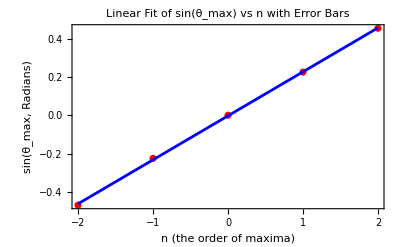

{0.229683,0.00206453}

```mathematica
(*Load the ErrorBarPlots package*)Needs["ErrorBarPlots`"];

(*Ensure the data is formatted as pairs of {x,y}*)
data=Transpose[{n1,sin}];

(*Fit the linear model using the variable x*)
model=LinearModelFit[data,x,x];

(*Combine n,sin(θ_max),and errors*)dataErrorBars=Transpose[{n1,sin,dsin}];

(*Generate error list plot*)
Show[ErrorListPlot[dataErrorBars,PlotStyle->Red,PlotRange->Full],Plot[model[x],{x,Min[n1],Max[n1]},PlotStyle->Blue],Frame->True,FrameLabel->{"n (the order of maxima)","sin(θ_max, Radians)"},PlotLabel->"Linear Fit of sin(θ_max) vs n with Error Bars"]

(*Display the results*)
{slope,slopeError}={model["BestFitParameters"][[2]],model["ParameterErrors"][[2]]};

(*Results*)
{slope,slopeError}
```

- What does the slope of the fitting line represent? Using your measured value for d find another estimation for wavelength from this interference experiment, which we call λ_i. The subscript i is used for interference. Show your work on how you calculate Δλ_i here, using Δslope.
- Compare λ_i to the wavelength measurement using the oscilloscope, λ_o.
- Record the result on the table below.

Answer:
the slope cant be interpreted as the change in the value of the sine of the angle between the center of the transmitters and the receiver as the number of maximums the receiver is away from 0 degrees increases. or more physically the slope is the change in the phase difference of the sound waves as a function of the path difference between the two sound waves

Wavelength (λi): 0.00689049 meters
Error in Wavelength (Δλi): 0.000061938 meters
Wavelength measured using oscilloscope (λ_o): 0.0085 meters

Thus the error in λi = 18.9354% as compared to λ_o

There were several reasons for this. Once being that the deviations with increasing lambda were really faint. They were also very sensitive to any hand movement which may have caused errors in addition to other possible measurement and apparatus error.

```mathematica
(* This is an Input cell in case you need *)
(*Define the measured values*)
slope;
slopeError;
d=0.037; (*Distance in meters*)

(*Calculate the wavelength (λ_i)*)
lambdai=slope*d

(*Calculate the error in the wavelength (Δλ_i) using error propagation*)
lambdaiError=slopeError*d;

lambdao = N[lambdaO/1000]
(*Display the results*)
Print["Wavelength (λ_i): ",lambdai," meters"];
Print["Error in Wavelength (Δλ_i): ",lambdaiError," meters"];
Print["Wavelength measured using oscilloscope (λ_o): ",lambdao," meters"];

(lambdao-lambdai)/lambdao*100

(*Calculate the ratio λ_i/λ_o*)
ratio=lambdai/lambdao;
lambdaiError/lambdai
deltalambdao/lambdao
(*Calculate the relative error in the ratio Δ(λ_i/λ_o) using error propagation*)
relativeError=Sqrt[(lambdaiError/lambdai)^2+(deltalambdao/lambdao)^2]*ratio
```

0.00849826

0.0085

Wavelength (λ_i): 0.00849826 meters

Error in Wavelength (Δλ_i): 0.0000763876 meters

Wavelength measured using oscilloscope (λ_o): 0.0085 meters

0.0205051

0.00898861

16.6378

16.6344

```mathematica
Grid[{{Text["Table 5. Comparing Wavelength Results"],SpanFromLeft},
{"slope±Δslope","λ_i±Δλ_i (mm)","λ_i/λ_o±Δ(λ_i/λ_o)"},
{PlusMinus[slope,slopeError],PlusMinus[lambdai*1000,lambdaiError],PlusMinus[ratio,relativeError]}
},Frame->All]
```

Table 5. Comparing Wavelength Results |  | 
slope±Δslope | λ_i±Δλ_i (mm) | λ_i/λ_o±Δ(λ_i/λ_o)
0.229683±0.00206453 | 8.49826±0.0000763876 | 0.999795±16.6344

### Step 2.

Now we will use a setup with a different geometry where equation (2) does not apply. As shown in fig. 4, the two transmitters are separated with a distance d, and the receiver at P is sitting at a distance z from S_1 and S_1 S_2 ⊥ S_1P.

Figure 4. The geometry of the experiment with two transmitters for double source interference, step 2.

-Graphics-

- Use equation (1) to find the formulas below for theoretical d_max and d_min, corresponding to maximum and minimum intensity at P.
(3)	d_max=√(n λ(n λ+2z)),	d_min=√((n+1/2)λ [(n+1/2)λ+2z]).

Hint:
> For the minimums, the difference between the paths must be (n+1/2)λ, in other words the waves from S_1 and S_2 arrive at P with π phase difference.

Answer:
Put your work here.
d = 9.9cm
z = 11.3cm
S1P=z
S2P=N[Sqrt[d^2 + z^2]] = 15.0233

```mathematica
(* This is an Input cell in case you need *)
d=9.9(*cm*)
z=11.3(*cm*)
S1P=z
S2P=N[Sqrt[d^2+z^2]]
```

9.9

11.3

11.3

15.0233

Now, keeping S_1 and P fixed and in front of each other, we want to vary the separation d and record the values of d for which maxima and minima in intensity are observed at the receiver.
The  mount that the sources S_1 and S_2 are screwed on, is attached to the board by a magnet. So you can easily move it so that the S_1 source and the receiver P are right in front of each other.
To vary d, you can loosen the screw that keeps S_2 on the mount and carefully rotate the S_2 source. Do not loosen the screw too much, as it might cause the S_2 to wobble. Do not loosen it too little, because if it is too tight and you try to rotate, you might move the whole mount.
Mark the position of the mount with a pencil or something. This way you’d know if it displaces in the middle of the measurements, and you can fix it back.

Figure 5. The setup of the experiment with two transmitters for double source interference, step 2.

-Graphics-

- Choose a fixed value for z. Run the cell below to set the value for z variable.

```mathematica
z=10; (10 ± 1 mm *)
```

- Now vary d and copy your measurements of maxima and minima in the code below, and run the code cells after filling the tables.
The codes will do a nonlinear fit of d_max and d_min in terms of n, using the equation (3). There is also an extra intercept parameter b which compensate some of the possible offset errors. b must be much smaller than d values.

Hints:
> If there is no squares available, you can use a piece of paper as your reference for making S_1 S_2 and S_1P perpendicular. Be sure that the geometry is the same as figure 4.
> Do not choose a z that is smaller than 8cm or bigger than 17 cm. You want the separation between the minima and maxima to be large so that measurements are more reliable. But you also want these separations small enough so that you can have more number of data points (Because the dynamic range for d, i.e. the range that d can vary, is limited. d can change from 2.5 cm to about 15 cm.).
> To estimate the errors Δ d_max or Δ d_min try to move back and forth and examine how sharp you can decide on that specific minimum or maximum. A typical value is about two mm.

```mathematica
d=7.4
```

7.4

FittedModel[…]

| Estimate | Standard Error | Confidence Interval
lambda1 | 13.3415 | 0.0557159 | {13.1982,13.4847}
b1 | 17.6854 | 0.249296 | {17.0446,18.3263}

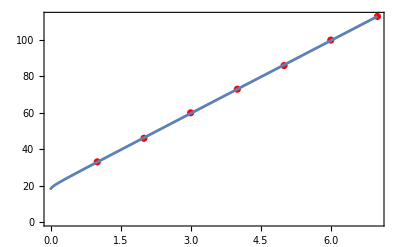

```mathematica
ndmax=Rest[{{"n", "d_max^EXP (mm)", "Δd_max^EXP (mm)"}, {1, 33, 1}, {2, 46, 1}, {3, 60, 1}, {4, 73, 1}, {5, 86, 1}, {6, 100, 1}, {7, 113, 1}}];
n2 = ndmax[[All, 1]];
dmax=ndmax[[All,2]];
ddmax=ndmax[[All,3]];

dmax2vn = Table[{n2[[i]],dmax[[i]]},{i,1,Length[n2]}];
line1= NonlinearModelFit[dmax2vn,Sqrt[lambda1*(n)*(lambda1(n) + 2*z)]+b1,{lambda1,b1},n]
line1["ParameterConfidenceIntervalTable"]

Needs["ErrorBarPlots`"];

dmax2vnerr = Table[{n2[[i]],dmax[[i]],ddmax[[i]]},{i,1,Length[n2]}];
Show[
ErrorListPlot[dmax2vnerr,PlotStyle->Red],
Plot[line1[n],{n,0,Max[n2]}],
Frame->True]
```

FittedModel[…]

| Estimate | Standard Error | Confidence Interval
lambda2 | 6.86026 | 0.658073 | {5.16863,8.55189}
b2 | 6.13284 | 4.24263 | {-4.77319,17.0389}

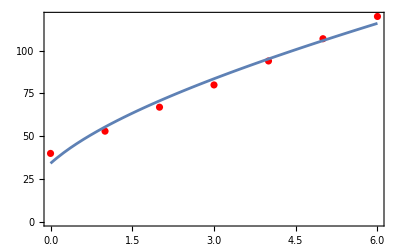

```mathematica
ndmin=Rest[{{"n", "d_min^EXP (mm)", "Δd_min^EXP (mm)"}, {0, 40, 1}, {1, 53, 1}, {2, 67, 1}, {3, 80, 1}, {4, 94, 1}, {5, 107, 1}, {6, 120, 1}}];
n2 = ndmin[[All, 1]];
dmin=ndmin[[All,2]];
ddmin=ndmin[[All,3]];

dmin2vn = Table[{n2[[i]],dmin[[i]]},{i,1,Length[n2]}];
line2= NonlinearModelFit[dmin2vn,Sqrt[lambda2*(n+1/2)*(lambda2*(n+1/2) + 2*z)]+b2,{lambda2,b2},n]
line2["ParameterConfidenceIntervalTable"]

Needs["ErrorBarPlots`"];

dmin2vnerr = Table[{n2[[i]],dmin[[i]],ddmin[[i]]},{i,1,Length[n2]}];
Show[
ErrorListPlot[dmin2vnerr,PlotStyle->Red],
Plot[line2[n],{n,0,Max[n2]}],
Frame->True]
```

If you look at the equation (3) you can see that the fit parameters above are λ and b. b is an offset error which takes care of a constant offset error of the experiment.
For example, this offset can can compensate some parts of heights or angles of the transmitters not being the same.
We call the estimation of wavelength in this section λ_p where p stands for perpendicular geometry we have used here.

- Find another estimation for the wavelength, λ_p±Δ λ_p, using lambda1 and lambda2 fit parameters above.
- Record the results on the table below.

Answer:
Put your work here.

```mathematica
(* This is an Input cell in case you need *)
(*Define the fit parameters and their standard errors*)lambda1=13.3415;
lambda1Error=0.0557159;
lambda2=6.8602614030557545;
lambda2Error=0.6580728901095966;

(*Calculate the estimated wavelength (λ_p)*)
lambdap=(lambda1+lambda2)/2/1000;

(*Calculate the error in the wavelength (Δλ_p) using error propagation*)
lambdapError=Sqrt[(lambda1Error/2)^2+(lambda2Error/2)^2]/1000;

(*Calculate the ratio λ_p/λ_o*)
ratio=lambdap/lambdao;

(*Calculate the relative error in the ratio Δ(λ_p/λ_o) using error propagation*)
relativeError=(lambdapError/lambdap)*ratio;

(*Display the results*)
Print["Estimated Wavelength (λ_p): ",lambdap," milli meters"];
Print["Error in Estimated Wavelength (Δλ_p): ",lambdapError," milli meters"];
```

Estimated Wavelength (λ_p): 0.0101009 milli meters

Error in Estimated Wavelength (Δλ_p): 0.000330214 milli meters

```mathematica
Grid[{{Text["Table 6. Using geometry of fig.4 to estimate wavelength"],SpanFromLeft},
{"λ_p±Δλ_p (mm)","λ_p/λ_o±Δ(λ_p/λ_o)"},
{PlusMinus[lambdap,lambdapError],PlusMinus[ratio,relativeError]}
},Frame->All]
```

Table 6. Using geometry of fig.4 to estimate wavelength | 
λ_p±Δλ_p (mm) | λ_p/λ_o±Δ(λ_p/λ_o)
0.0101009±0.000330214 | 1.18834±0.0388487

### Table X. Copy All Your Final Results.

```mathematica
Grid[{{Text["Table X. All Final Results Gathered"],SpanFromLeft},
{"f_o±Δf_o (kHz)","λ_o±Δλ_o (mm)","λ_i±Δλ_i (mm)","λ_p±Δλ_p (mm)"},
{PlusMinus[fo,deltaFo],
PlusMinus[lambdao*1000,N[deltaLambdaO*1000]],
PlusMinus[lambdai*1000,lambdaiError*1000],
PlusMinus[lambdap*1000,lambdapError*1000]}
},Frame->All]
```

Table X. All Final Results Gathered |  |  | 
f_o±Δf_o (kHz) | λ_o±Δλ_o (mm) | λ_i±Δλ_i (mm) | λ_p±Δλ_p (mm)
40000±0.399969 | 8.5±141.421 | 6.89049±0.061938 | 10.1009±0.330214

Rutgers 276 Classical Physics Lab
“Interference of Sound Waves”
Copyright 2017 Roshan Tourani and Girsh Blumberg